```mathematica
Limit[Sin[n x]/x,x->0]
```

n

```mathematica
F[w_]:=∫_-n^n ⅇ^(-I w t)ⅆt
```

```mathematica
TrigReduce[F[w]]
```

```mathematica
G[n_,w_]:=(2n Sin[n w])/(n w)
```

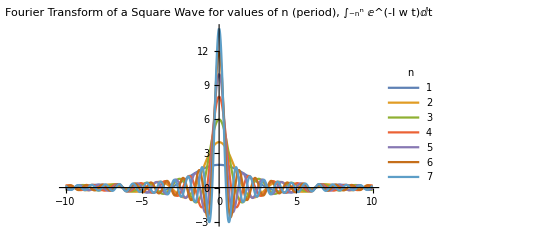

```mathematica
Plot[Evaluate@Table[G[n,w],{n,1,7}],{w,-10,10},PlotLabel->"Fourier Transform of a Square Wave for values of n (period), ∫_-n^n ⅇ^(-I w t)ⅆt",PlotLegends->LineLegend[Table[n,{n,1,7}],LegendLabel->n],PlotRange->All]
```